First, we set the dimension d and prepare the target average state

```mathematica
d=17;
mean=Join[Array[x,d],Flatten[KroneckerProduct[#,#]&[Array[x,d]]]]/.{x[i_]^2:>Binomial[d+1,2]^-1,x[i_]x[j_]:>1/2 Binomial[d+1,2]^-1}/.x[j_]:>d^-1//N;
```

Definitions of auxiliary functions - decoherence of the states with respect to the computational basis and cost function to be minimized

```mathematica
proj[state_]:=Abs[state]^2
costFunc[unit_]:=Norm[Mean[Join[#,Flatten[KroneckerProduct[#,#]]]&[proj[#]]&/@unit]-mean]
```

Non-optimal code, which utilizes random walk approach to find bases which decohere to a simplex 2-design. The code has been tested for dimensions up to 42.

```mathematica
stepSize=1.
error=0

start=RandomVariate[CircularUnitaryMatrixDistribution[d]];
startCost=costFunc[start]
threshold=10^-12
Monitor[While[Chop[startCost,threshold]>0,step=MatrixExp[I stepSize RandomVariate[GaussianUnitaryMatrixDistribution[d]]];
newCost=costFunc[step.start];
If[newCost<startCost,startCost=newCost;start=step.start;error=0,error+=1];
If[error>100,error=0;stepSize=stepSize/2];
If[Chop[stepSize,10^-3 threshold]==0,stepSize=1.;start=RandomVariate[CircularUnitaryMatrixDistribution[d]];
startCost=costFunc[start]]],{startCost,stepSize,error}]
```

1.

0

0.0101827

1/1000000000000

Explicit form of the basis, provided below in a graphical form - the absolute values and the arguments of all the entries

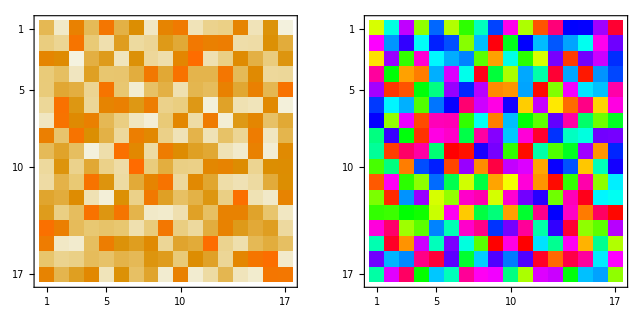

```mathematica
GraphicsRow[{MatrixPlot[Abs[start]],MatrixPlot[Arg[start],ColorFunction->(Hue[Mod[#,2Pi]/(2Pi)]&),ColorFunctionScaling->False]}]
```